# Refraction through a lens (no approximations)

The two surface of the lens are takes to be circles. This can be changes so that the two bounding surface are any smooth curves.

### Notation

```mathematica
<<Notation`
Symbolize[Subscript[x_, y_]]
Symbolize[UnderBar[x_]]
Notation[x_⊗y_ ⟺ DyadicProduct[x_,y_]]
```

### Subroutines

```mathematica
ClearAll["Global`*"]
UnderBar[Ι̲]={{1,0},{0,1}};
DyadicProduct[x_,y_]:=
Module[{n=Length[x]},
Table[x[[i]]y[[j]],{i,1,n},{j,1,n}]]
s1[x_]:=s1[Unevaluated[x]]
r1[x_]:=r1[Unevaluated[x]]
s2[x_]:=s1[Unevaluated[x]]
r2[x_]:=r1[Unevaluated[x]]


ClearAll[DrawRay,yl,Intersect,DrawSurf,Computemc]

yl[x_,m_,c_]:= m x +c;

DrawRay[r_/;r["type"]=="ray",color_:Red,details_:"False"]:=Module[{data,p1,p2},
p1=r["pt1"];
p2=r["pt2"];
If[details=="True",
Graphics[{color,Arrow[{p1,p2}]}],
Graphics[{color,Line[{p1,p2}]}]]
]

DrawSurf[s_/;s["type"]=="surface"]:=Module[
{data},
Graphics@Circle[s["origin"],s["radius"]]
]


Ray[{x1_:0.0,y1_:0.0},{x2_:0.0,y2_:0.0},slope_:"EMPTY"]:=
Module[{θ,r,m,c},
If[slope=="EMPTY",
r=<|"pt1"->{x1,y1},"pt2"->{x2,y2}, "type"->"ray"|>;
{m,c}=Computemc[r];
r["slope"]=m;
r,
θ=ArcTan[slope]//N;
<|"pt1"->{x1,y1},"pt2"->{x1,y1}+{Cos[θ],Sin[θ]},"slope"->slope, "type"->"ray"|>
]]

Computemc[ry_/;ry["type"]=="ray"]:=Module[{sol,m,c,x1,y1,x2,y2},
{x1,y1}=ry["pt1"];
{x2,y2}=ry["pt2"];
{m,c}/.(Solve[yl[x1,m,c]==y1 && yl[x2,m,c]==y2,{m,c},Reals] [[1]])
]


Intersect[ry_/;ry["type"]=="ray", s_/; s["type"]=="surface",motion_:"Entering"]:=Module[{m,c,x1,y1,x2,y2,ox,oy,r,x,y,sol},
{ox,oy}=s["origin"];
r=s["radius"];
{m,c}=Computemc[ry];
sol={x,y}/.NSolve[ (x-ox)^2+ (y-oy)^2==r^2 && yl[x,m,c]==y, {x,y} ];
If[motion=="Entering",
If[sol[[1,1]]<sol[[2,1]],sol[[1]],sol[[2]]],
If[sol[[1,1]]>sol[[2,1]],sol[[1]],sol[[2]]]
]
]

dir[ry_/;ry["type"]=="ray"]:=Module[{pt1,pt2,d},
pt1=ry["pt1"];
pt2=ry["pt2"];
d=(pt2-pt1);
d/Norm[d]
]


RefractDirection[N̲:_,UnderBar[s1]:_,Subscript[n, 1]:_,Subscript[n, 2]:_]:=Module[{UnderBar[P̲],r=Subscript[n, 1]/Subscript[n, 2]},
UnderBar[P̲]=(N̲⊗N̲ );
r(UnderBar[Ι̲]-UnderBar[P̲]).UnderBar[s1]-(1-r^2(1-UnderBar[s1].(UnderBar[P̲].UnderBar[s1])))^(1/2)N̲]

ComputeNormal[s_/; s["type"]=="surface",p_,motion_:"Entering"]:=Module[{c,n},
c=s["origin"];
If[motion=="Entering",Normalize[p-c],-Normalize[p-c]]
]

ClearAll[Refract]
Refract[ry_/;ry["type"]=="ray", s_/; s["type"]=="surface",motion_:"Entering"]:=Module[{p,n,ry1,ry2,d1,Subscript[n, 1],Subscript[n, 2]},
If[motion=="Entering",Subscript[n, 1]=1;Subscript[n, 2]=s[μ],Subscript[n, 1]=s[μ];Subscript[n, 2]=1];
p=Intersect[ry,s,motion];
ry1=Ray[ry["pt1"],p];
n=ComputeNormal[s,p,motion];
ry2=Ray[p,p+RefractDirection[n,dir[ry1],Subscript[n, 1],Subscript[n, 2]]];
{ry1,ry2,n,p}
]

ClearAll[PlotRays]
PlotRays[r1_,r2_,s_,n_,p_]:=Module[{},
Show[Graphics@Point[p],Graphics[{Dashed,Red,Line[{p,p+dir[r1]}]}],DrawRay[r1,Red],DrawRay[r2,Green],DrawSurf[s],
Graphics[{Gray,Arrow[{p,p+n}]}],
Graphics[{Dashed,Gray,Line[{p,p-n}]}]
]
]



PlotRays2[r1_,r2_,n_,p_,details_:"Flase"]:=Module[{},

If[details=="True",
Show[Graphics@Point[p],Graphics[{Dashed,Red,Line[{p,p+dir[r1]}]}],DrawRay[r1,Red],DrawRay[r2,Green],
Graphics[{Gray,Arrow[{p,p+n}]}],
Graphics[{Dashed,Gray,Line[{p,p-n}]}]
],
Show[Graphics@Point[p],DrawRay[r1,Red,details],DrawRay[r2,Green,details]
]
]
]

PlotLens[s1_,s2_]:=Module[{},
Region@RegionIntersection[
Disk[s1["origin"],s1["radius"]],
Disk[s2["origin"],s2["radius"]]
]
]


ScaleRay[ry_,α_]:=Module[{pt1,pt2,l,d},
pt1=ry["pt1"];
pt2=ry["pt2"];
l=Norm[pt1-pt2];
d=dir[ry];
<|"pt1"->pt1,"pt2"->pt1+α l d, "slope"->ry["slope"],"type"->"ray"|>]


ClearAll[ShowPath]
ShowPath[x_:-10.0,y_:0,slope_:0.0,s1_,s2_,α_:1,details_:"False"]:=Module[{r1,r2,r3,n1,p1,n2,p2,plt1,plt2,rad1},
rad1=s1["radius"];
r1=Ray[{x,y},{0,0},slope];
{r1,r2,n1,p1}=Refract[r1,s1,"Entering"];
plt1=PlotRays2[r1,ScaleRay[r2,α],n1,p1,details];
{r2,r3,n2,p2}=Refract[r2,s2,"Leaving"];
plt2=PlotRays2[r2,ScaleRay[r3,α],n2,p2,details];
{plt1,plt2}
]
```

```mathematica
Unprotect[s1,s2]
ClearAll[s1,s2,r1,r2,r3,n1,n2,p1,p2];
s1=<|"origin"->{0.0,0},"radius"->2,μ->1.5, "type"->"surface"|>;
s2=<|"origin"->{0.0,0.0},"radius"->2,μ->1.5, "type"->"surface"|>;
(*Protect[s1,s2];*)
r1=Ray[{-5.0,1},{0.0,1}];
{r1,r2,n1,p1}=Refract[r1,s1,"Entering"];
{r2,r3,n2,p2}=Refract[r2,s2,"Leaving"];
```

{}

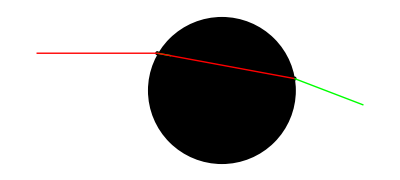

```mathematica
plt1=PlotRays2[r1,ScaleRay[r2,0.1],n1,p1];
plt2=PlotRays2[r2,ScaleRay[r3,2],n2,p2];
lens=PlotLens[s1,s2];
Show[lens,plt1,plt2]
```

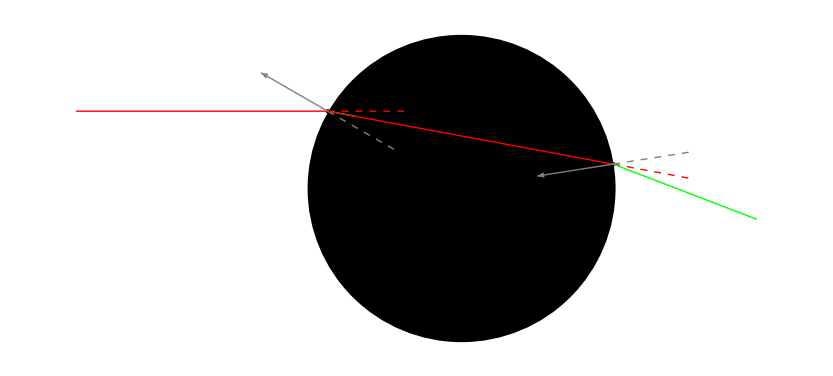

```mathematica
plt1=PlotRays2[r1,ScaleRay[r2,0.1],n1,p1,"True"];
plt2=PlotRays2[r2,ScaleRay[r3,2],n2,p2,"True"];
Show[lens,plt1,plt2]
```

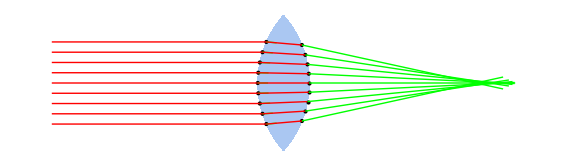

```mathematica
s1=<|"origin"->{0.0,0},"radius"->1,μ->1.25, "type"->"surface"|>;
s2=<|"origin"->{-1.5,0.0},"radius"->1,μ->1.25, "type"->"surface"|>;
lens=PlotLens[s1,s2];
Show[lens,
Table[ShowPath[-3.,y,0,s1,s2,0.1][[1]],{y,Range[-0.4,0.4,0.1]}],
Table[ShowPath[-3.,y,0,s1,s2,2][[2]],{y,Range[-0.4,0.4,0.1]}]

]
```

History

```mathematica
(*ClearAll[Refract]
Refract[ry_/;ry["type"]=="ray", s_/; s["type"]=="surface",motion_:"Entering"]:=Module[{Subscript[i, p],Subscript[i, r],n,Subscript[m, i],Subscript[c, p],Subscript[θ, i],Subscript[θ, r],Subscript[d, r],normal},
Subscript[i, p]=ry["pt2"];
Subscript[c, p]=s["origin"];
Echo[{Subscript[i, p],Subscript[c, p]}];
If[motion=="Entering",
normal=dir[Ray[Subscript[c, p],Subscript[i, p]]];
Subscript[θ, i]=RotAngle[-normal,dir[ry]];
Subscript[θ, r]=ArcSin[Sin[Subscript[θ, i]]/s[μ]];
Echo[Subscript[θ, i],"Entering, θ_i"];
Echo[Subscript[θ, r],"Entering,θ_r"];,


normal=dir[Ray[Subscript[i, p],Subscript[c, p]]];
Subscript[θ, i]=RotAngle[-normal,dir[ry]];
Subscript[θ, r]=ArcSin[Sin[Subscript[θ, i]]*s[μ]];
Echo[Subscript[θ, i],"Leaving, θ_i"];
Echo[Subscript[θ, r],"Leaving,θ_r"];
If[Abs[Subscript[θ, r]]≥ π/2,Echo["θ_r>=π/2"],Continue]
];

Echo[Subscript[θ, i] Subscript[θ, r]];
Subscript[d, r]=RotationMatrix[Subscript[θ, r]].(-normal);
(*Subscript[i, r]=Ray[Subscript[i, p],Subscript[i, p]+3 Subscript[d, r]]*)
Ray[Subscript[i, p],Subscript[i, p]+3 Subscript[d, r]]
]*)




(*UnderBar[Ι̲]={{1,0,0},{0,1,0},{0,0,1}};*)

(*motion="Leaving"
s=s2;
Subscript[n, 1]=1.2;


Subscript[n, 2]=1;
p=Intersect[r2,s,motion]
r2["pt2"]=p;
n=ComputeNormal[s,p,motion];
r3=Ray[p,p+RefractDirection[n,dir[r2],Subscript[n, 1],Subscript[n, 2]]];
*)



ClearAll[RotAngle]
(*RotAngle[u_/;VectorQ[u],v_/;VectorQ[v]]:=Module[{θ,u1=u[[1]],u2=u[[2]],v1=v[[1]],v2=v[[2]],x},
(*x=θ/.{FindRoot[{u1 Cos[θ]-u2 Sin[θ]==v1,},{θ,0.0001}],
FindRoot[{u2 Cos[θ]+u1 Sin[θ]==v2 },{θ,0.0001}]};
If[Abs[x[[1]]]<Abs[x[[2]]],x[[1]],x[[2]]]
*)
{θ,r}/.NSolve[{u1 Cos[θ]-u2 Sin[θ]== r v1,
  u2 Cos[θ]+u1 Sin[θ]==r v2 },{θ,r}][[1]]
]
*)RotAngle[u_/;VectorQ[u],v_/;VectorQ[v]]:=Module[{},
Cross[Flatten[{u,0}],Flatten[{v,0.0}]][[3]]ArcCos[(u/Norm[u]).(v/Norm[v])]]




(*Intersect[ry_/;ry["type"]=="ray", s_/; s["type"]=="surface"]:=Module[{m,c,x1,y1,x2,y2,ox,oy,r,x,y,sol},
{ox,oy}=s["origin"];
r=s["radius"];
{m,c}=Computemc[ry];
sol={x,y}/.NSolve[ (x-ox)^2+ (y-oy)^2==r^2 && yl[x,m,c]==y, {x,y} ];
If[sol[[1,1]]<sol[[2,1]],sol[[1]],sol[[2]]]
]
*)



(*
motion="Entering"
s=s1;
Subscript[n, 1]=1;
Subscript[n, 2]=1.2;
p=Intersect[r1,s,motion];
r1["pt2"]=p;
n=ComputeNormal[s,p,motion];
r2=Ray[p,p+RefractDirection[n,dir[r1],Subscript[n, 1],Subscript[n, 2]]];
*)
```